```mathematica
Table[1000,5]
```

{1000,1000,1000,1000,1000}

6.2:

```mathematica
Table[n^3,{n,10,20}]
```

{1000,1331,1728,2197,2744,3375,4096,4913,5832,6859,8000}

6.3:

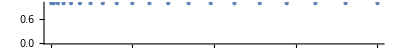

```mathematica
NumberLinePlot[Table[n^2,{n,20}]]
```

6.4

```mathematica
Table[n,{n,2,20,2}]
```

{2,4,6,8,10,12,14,16,18,20}

6.5

```mathematica
Table[n,{n,10}]
```

{1,2,3,4,5,6,7,8,9,10}

6.6

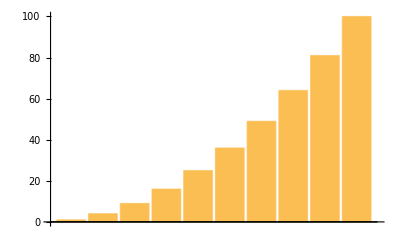

```mathematica
BarChart[Table[n^2,{n,10}]]
```

6.7

```mathematica
Table[IntegerDigits[n^2],{n,10}]
```

{{1},{4},{9},{1,6},{2,5},{3,6},{4,9},{6,4},{8,1},{1,0,0}}

6.8

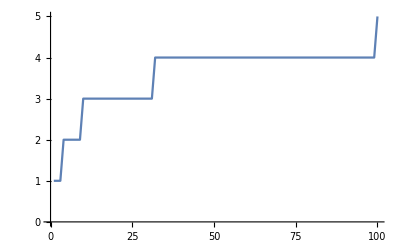

```mathematica
ListLinePlot[Table[Length[IntegerDigits[n^2]],{n,100}]]
```

6.9

```mathematica
Table[First[IntegerDigits[n^2]],{n,20}]
```

{1,4,9,1,2,3,4,6,8,1,1,1,1,1,2,2,2,3,3,4}

6.10

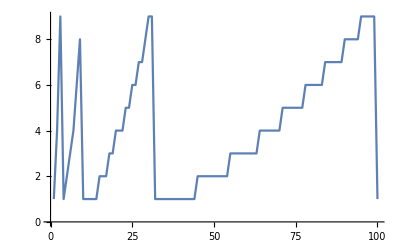

```mathematica
ListLinePlot[Table[First[IntegerDigits[n^2]],{n,100}]]
```

6.11:

```mathematica
Table[n^3-n^2,{n,10}]
```

{0,4,18,48,100,180,294,448,648,900}

This is really cool that when you find the last digit of differences between n^3 and n^2 that it starts with 0, 4, 8,8 and goes back to 0:

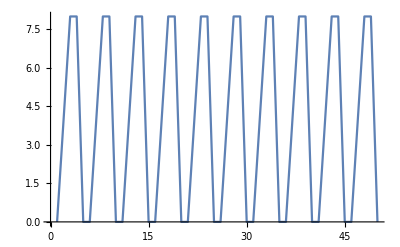

```mathematica
ListLinePlot[Table[Last[IntegerDigits[n^3-n^2]],{n,50}]]
```

6.12:

```mathematica
Table[n,{n,1,100,2}]
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99}

6.13:

```mathematica
Table[n^2,{n,2,100,2}]
```

{4,16,36,64,100,144,196,256,324,400,484,576,676,784,900,1024,1156,1296,1444,1600,1764,1936,2116,2304,2500,2704,2916,3136,3364,3600,3844,4096,4356,4624,4900,5184,5476,5776,6084,6400,6724,7056,7396,7744,8100,8464,8836,9216,9604,10000}

6.14:

```mathematica
Range[-3,2,1]
```

{-3,-2,-1,0,1,2}

6.15:

```mathematica
Table[Column[{n,n^2,n^3}],{n,20}]
```

{1
1
1,2
4
8,3
9
27,4
16
64,5
25
125,6
36
216,7
49
343,8
64
512,9
81
729,10
100
1000,11
121
1331,12
144
1728,13
169
2197,14
196
2744,15
225
3375,16
256
4096,17
289
4913,18
324
5832,19
361
6859,20
400
8000}

6.16:

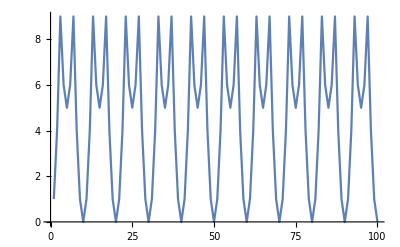

```mathematica
ListLinePlot[Table[Last[IntegerDigits[n^2]],{n,100}]]
```

```mathematica
Table[Last[IntegerDigits[n^2]],{n,100}]
```

{1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0}

6.17:

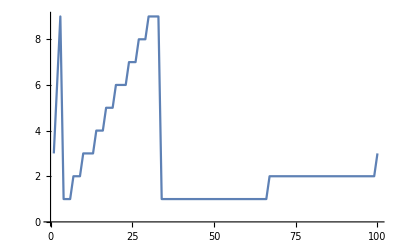

```mathematica
ListLinePlot[Table[First[IntegerDigits[n*3]],{n,100}]]
```

```mathematica
Table[First[IntegerDigits[n*3]],{n,100}]
```

{3,6,9,1,1,1,2,2,2,3,3,3,3,4,4,4,5,5,5,6,6,6,6,7,7,7,8,8,8,9,9,9,9,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3}

6.18:

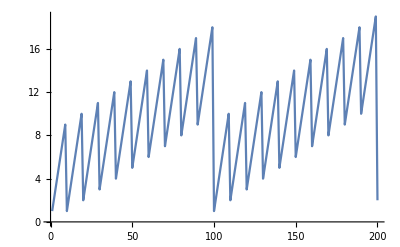

```mathematica
ListLinePlot[Table[Total[IntegerDigits[n]],{n,200}]]
```

```mathematica
Table[Total[IntegerDigits[n]],{n,200}]
```

{1,2,3,4,5,6,7,8,9,1,2,3,4,5,6,7,8,9,10,2,3,4,5,6,7,8,9,10,11,3,4,5,6,7,8,9,10,11,12,4,5,6,7,8,9,10,11,12,13,5,6,7,8,9,10,11,12,13,14,6,7,8,9,10,11,12,13,14,15,7,8,9,10,11,12,13,14,15,16,8,9,10,11,12,13,14,15,16,17,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7,8,9,10,2,3,4,5,6,7,8,9,10,11,3,4,5,6,7,8,9,10,11,12,4,5,6,7,8,9,10,11,12,13,5,6,7,8,9,10,11,12,13,14,6,7,8,9,10,11,12,13,14,15,7,8,9,10,11,12,13,14,15,16,8,9,10,11,12,13,14,15,16,17,9,10,11,12,13,14,15,16,17,18,10,11,12,13,14,15,16,17,18,19,2}

6.19

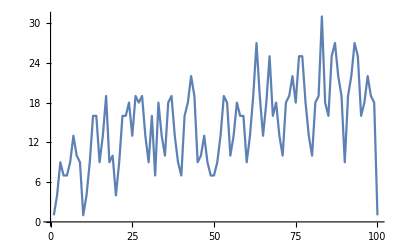

```mathematica
ListLinePlot[Table[Total[IntegerDigits[n^2]],{n,100}]]
```

6.20

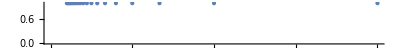

```mathematica
NumberLinePlot[Table[1/n,{n,20}]]
```

6.21

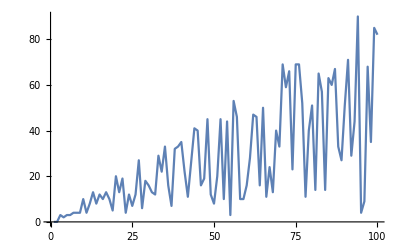

```mathematica
ListLinePlot[Table[RandomInteger[{0,n}],{n,100}]]
```

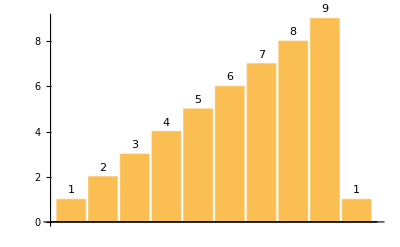

```mathematica
BarChart[Table[Total[IntegerDigits[n]],{n,1,10}], ChartLabels->Placed[Table[Total[IntegerDigits[n]],{n,1,10}],Above]]
```

```mathematica
Manipulate[functionToGraph[Table[functionToCalculate[IntegerDigits[n^exp]],{n,1,end}]],{functionToGraph,{BarChart,ListPlot, ListLinePlot,NumberLinePlot}},{functionToCalculate,{Total,First,Last}},{end,1,100},{exp,{2,3,4,5,6}}]
```

```mathematica
Manipulate[Column[{Framed@Table[functionToCalculate[IntegerDigits[n^exp]],{n,1,number}],functionToGraph[Table[functionToCalculate[IntegerDigits[n^exp]],{n,1,number}]]}],{functionToGraph,{BarChart,ListPlot, ListLinePlot,NumberLinePlot}},{functionToCalculate,{Total,First,Last}},{number,1,100},{exp,{1,2,3,4,5,6}},FrameMargins->20]
```

```mathematica
Manipulate[functionToGraph[Table[functionToCalculate[IntegerDigits[n^exp]],{n,1,end}]],{functionToGraph,{BarChart,ListPlot, ListLinePlot,NumberLinePlot}},{functionToCalculate,{Total,First,Last}},{end,1,100},{exp,{2,3,4,5,6}}]
```